# MyFunction

One-line description explaining the function’s basic purpose

## Definition

```mathematica
ClearAll[MixedGraphToDirectedGraph]
MixedGraphToDirectedGraph[graph_?MixedGraphQ,options:OptionsPattern[]]:=WeightedAdjacencyGraph[Replace[Normal@Chop@WeightedAdjacencyMatrix[graph],{0->∞},{2}],options]
```

```mathematica
(*ClearAll[MixedGraphToDirectedGraph]
MixedGraphToDirectedGraph[graph_?MixedGraphQ]:=Graph[Join[EdgeList[graph,_->_],Join[DirectedEdge@@@(Reverse/@({First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_])),DirectedEdge@@{First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_]]],EdgeWeight->Join[Thread[Join[DirectedEdge@@@(Reverse/@({First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_])),DirectedEdge@@{First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_]]->Flatten[Transpose@Table[AnnotationValue[{graph,EdgeList[graph,_<->_]},EdgeWeight],2]]],Thread[EdgeList[graph,_->_]->AnnotationValue[{graph,EdgeList[graph,_->_]},EdgeWeight]]]]*)
```

```mathematica
GraphWeights[graph_?MixedGraphQ]:=Block[{undirectedWeights},undirectedWeights=Thread[(EdgeList[graph,_<->_]/.{u_<->v_->Sequence[u->v,v->u]})->Flatten[Transpose@Table[AnnotationValue[{graph,EdgeList[graph,_<->_]},EdgeWeight],2]]];Join[undirectedWeights,Thread[EdgeList[graph,_->_]->AnnotationValue[{graph,EdgeList[graph,_->_]},EdgeWeight]]]]
```

```mathematica
EdgeList[randomMixedGraph,_<->_]
```

{1<->2,2<->3,2<->4,2<->8,3<->8,3<->10,4<->8,4<->9,5<->10,6<->9}

```mathematica
EdgeList[randomMixedGraph,_<->_]/.{u_<->v_->Sequence[u->v,v->u]}
```

{1->2,2->1,2->3,3->2,2->4,4->2,2->8,8->2,3->8,8->3,3->10,10->3,4->8,8->4,4->9,9->4,5->10,10->5,6->9,9->6}

```mathematica
AnnotationValue[{randomMixedGraph,EdgeList[randomMixedGraph,_<->_]},EdgeWeight]
```

{0.479672,0.620412,0.0909199,0.406094,0.373012,0.00972539,0.857577,0.104675,0.409924,0.0522124}

```mathematica
Flatten[Transpose@Table[AnnotationValue[{randomMixedGraph,EdgeList[randomMixedGraph,_<->_]},EdgeWeight],2]]
```

{0.479672,0.479672,0.620412,0.620412,0.0909199,0.0909199,0.406094,0.406094,0.373012,0.373012,0.00972539,0.00972539,0.857577,0.857577,0.104675,0.104675,0.409924,0.409924,0.0522124,0.0522124}

```mathematica
Thread[(EdgeList[randomMixedGraph,_<->_]/.{u_<->v_->Sequence[u->v]})->Flatten[Transpose@Table[AnnotationValue[{randomMixedGraph,EdgeList[randomMixedGraph,_<->_]},EdgeWeight],2]]]
```

{1->2→0.479672,2->1→0.479672,2->3→0.620412,3->2→0.620412,2->4→0.0909199,4->2→0.0909199,2->8→0.406094,8->2→0.406094,3->8→0.373012,8->3→0.373012,3->10→0.00972539,10->3→0.00972539,4->8→0.857577,8->4→0.857577,4->9→0.104675,9->4→0.104675,5->10→0.409924,10->5→0.409924,6->9→0.0522124,9->6→0.0522124}

```mathematica
EdgeList[randomMixedGraph,_<->_]
```

{1<->2,2<->3,2<->4,2<->8,3<->8,3<->10,4<->8,4<->9,5<->10,6<->9}

```mathematica
{First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_]
```

{{1,2},{2,3},{2,4},{2,8},{3,8},{3,10},{4,8},{4,9},{5,10},{6,9}}

```mathematica
DirectedEdge@@{First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_]
```

{1->2,2->3,2->4,2->8,3->8,3->10,4->8,4->9,5->10,6->9}

```mathematica
(Reverse/@({First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_]))
```

{{2,1},{3,2},{4,2},{8,2},{8,3},{10,3},{8,4},{9,4},{10,5},{9,6}}

```mathematica
DirectedEdge@@@(Reverse/@({First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_]))
```

{2->1,3->2,4->2,8->2,8->3,10->3,8->4,9->4,10->5,9->6}

```mathematica
Join[DirectedEdge@@@(Reverse/@({First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_])),DirectedEdge@@{First[#],Last[#]}&/@EdgeList[randomMixedGraph,_<->_]]
```

{2->1,3->2,4->2,8->2,8->3,10->3,8->4,9->4,10->5,9->6,1->2,2->3,2->4,2->8,3->8,3->10,4->8,4->9,5->10,6->9}

```mathematica
Join[Thread[(EdgeList[randomMixedGraph,_<->_]/.{u_<->v_->Sequence[u->v,v->u]})->Flatten[Transpose@Table[AnnotationValue[{randomMixedGraph,EdgeList[randomMixedGraph,_<->_]},EdgeWeight],2]]],Thread[EdgeList[randomMixedGraph,_->_]->AnnotationValue[{randomMixedGraph,EdgeList[randomMixedGraph,_->_]},EdgeWeight]]]
```

{1->2→0.479672,2->1→0.479672,2->3→0.620412,3->2→0.620412,2->4→0.0909199,4->2→0.0909199,2->8→0.406094,8->2→0.406094,3->8→0.373012,8->3→0.373012,3->10→0.00972539,10->3→0.00972539,4->8→0.857577,8->4→0.857577,4->9→0.104675,9->4→0.104675,5->10→0.409924,10->5→0.409924,6->9→0.0522124,9->6→0.0522124,1->5→0.479672,1->8→0.620412,2->10→0.0909199,2->6→0.406094,2->9→0.373012,3->5→0.00972539,4->6→0.857577,6->10→0.104675,6->7→0.409924,7->10→0.0522124}

```mathematica
Length[%52]
```

30

```mathematica
MixedGraphToDirectedGraph[randomMixedGraph]
```

-Graphics-

```mathematica
FullForm[MixedGraphToDirectedGraph[randomMixedGraph]]
```

Graph[List[1,5,8,2,10,6,9,3,4,7],List[DirectedEdge[1,5],DirectedEdge[1,8],DirectedEdge[2,10],DirectedEdge[2,6],DirectedEdge[2,9],DirectedEdge[3,5],DirectedEdge[4,6],DirectedEdge[6,10],DirectedEdge[6,7],DirectedEdge[7,10],DirectedEdge[1,2],DirectedEdge[2,1],DirectedEdge[2,3],DirectedEdge[3,2],DirectedEdge[2,4],DirectedEdge[4,2],DirectedEdge[2,8],DirectedEdge[8,2],DirectedEdge[3,8],DirectedEdge[8,3],DirectedEdge[3,10],DirectedEdge[10,3],DirectedEdge[4,8],DirectedEdge[8,4],DirectedEdge[4,9],DirectedEdge[9,4],DirectedEdge[5,10],DirectedEdge[10,5],DirectedEdge[6,9],DirectedEdge[9,6]]]

```mathematica
FullForm[randomMixedGraph]
```

Graph[List[1,2,3,4,5,6,7,8,9,10],List[SparseArray[Automatic,List[10,10],0,List[1,List[List[0,2,5,6,7,7,9,10,10,10,10],List[List[5],List[8],List[10],List[6],List[9],List[5],List[6],List[10],List[7],List[10]]],List[1,1,1,1,1,1,1,1,1,1]]],SparseArray[Automatic,List[10,10],0,List[1,List[List[0,1,4,6,8,9,10,10,10,10,10],List[List[2],List[3],List[4],List[8],List[8],List[10],List[8],List[9],List[10],List[9]]],List[1,1,1,1,1,1,1,1,1,1]]]],List[Rule[EdgeWeight,List[0.479672,0.620412,0.0909199,0.406094,0.373012,0.00972539,0.857577,0.104675,0.409924,0.0522124,0.188831,0.699409,0.38598,0.569382,0.586719,0.674689,0.061344,0.3073,0.261188,0.00131874]],Rule[GraphLayout,List[Rule["Dimension",2]]],Rule[VertexLabels,List[Automatic]]]]

```mathematica
InputForm[randomMixedGraph]
```

Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, 
 {SparseArray[Automatic, {10, 10}, 0, {1, {{0, 2, 5, 6, 7, 7, 9, 10, 10, 10, 10}, {{5}, 
     {8}, {10}, {6}, {9}, {5}, {6}, {10}, {7}, {10}}}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1}}], 
  SparseArray[Automatic, {10, 10}, 0, {1, {{0, 1, 4, 6, 8, 9, 10, 10, 10, 10, 10}, {{2}, 
     {3}, {4}, {8}, {8}, {10}, {8}, {9}, {10}, {9}}}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1}}]}, 
 {EdgeWeight -> {0.4796719103853646, 0.6204119214370416, 0.09091986628481452, 
   0.40609383449669667, 0.373011723623091, 0.009725387306362965, 0.8575769884907003, 
   0.1046749128993445, 0.40992358984551447, 0.05221240070847655, 0.18883081253083134, 
   0.6994093241653807, 0.38597953585065303, 0.5693817546492557, 0.5867185882383155, 
   0.6746885964681018, 0.061343980674861465, 0.307300496033011, 0.26118808535738824, 
   0.001318744216778578}, GraphLayout -> {"Dimension" -> 2}, VertexLabels -> {Automatic}}]

```mathematica
MixedGraphToDirectedGraph[randomMixedGraph]
```

-Graphics-

```mathematica
AnnotationValue[MixedGraphToDirectedGraph[randomMixedGraph],EdgeWeight]
```

{0.479672,0.620412,0.0909199,0.406094,0.373012,0.00972539,0.857577,0.104675,0.409924,0.0522124,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
InputForm[MixedGraphToDirectedGraph[randomMixedGraph]]
```

Graph[{1, 5, 8, 2, 10, 6, 9, 3, 4, 7}, {DirectedEdge[1, 5], DirectedEdge[1, 8], 
  DirectedEdge[2, 10], DirectedEdge[2, 6], DirectedEdge[2, 9], DirectedEdge[3, 5], 
  DirectedEdge[4, 6], DirectedEdge[6, 10], DirectedEdge[6, 7], DirectedEdge[7, 10], 
  DirectedEdge[1, 2], DirectedEdge[2, 1], DirectedEdge[2, 3], DirectedEdge[3, 2], 
  DirectedEdge[2, 4], DirectedEdge[4, 2], DirectedEdge[2, 8], DirectedEdge[8, 2], 
  DirectedEdge[3, 8], DirectedEdge[8, 3], DirectedEdge[3, 10], DirectedEdge[10, 3], 
  DirectedEdge[4, 8], DirectedEdge[8, 4], DirectedEdge[4, 9], DirectedEdge[9, 4], 
  DirectedEdge[5, 10], DirectedEdge[10, 5], DirectedEdge[6, 9], DirectedEdge[9, 6]}, 
 {EdgeWeight -> {0.4796719103853646, 0.6204119214370416, 0.09091986628481452, 
    0.40609383449669667, 0.373011723623091, 0.009725387306362965, 0.8575769884907003, 
    0.1046749128993445, 0.40992358984551447, 0.05221240070847655, 1, 1, 1, 1, 1, 1, 1, 1, 
    1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}}]

```mathematica
EdgeCount[randomMixedGraph]
```

20

```mathematica
EdgeCount[MixedGraphToDirectedGraph[randomMixedGraph]]
```

30

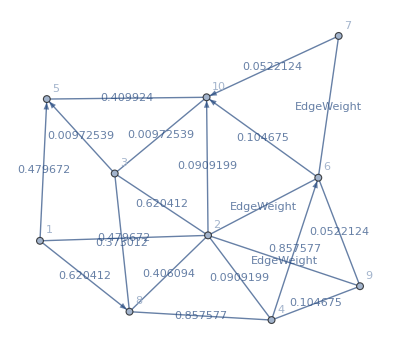

```mathematica
Graph[randomMixedGraph,EdgeLabels->"EdgeWeight"]
```

```mathematica
WeightedAdjacencyMatrix[MixedGraphToDirectedGraph[randomMixedGraph]]
```

SparseArray[…]

```mathematica
WeightedAdjacencyMatrix[Graph[MixedGraphToDirectedGraph[randomMixedGraph],EdgeWeight->{1->2->0.4796719103853646,2->1->0.4796719103853646,2->3->0.6204119214370416,3->2->0.6204119214370416,2->4->0.09091986628481452,4->2->0.09091986628481452,2->8->0.40609383449669667,8->2->0.40609383449669667,3->8->0.373011723623091,8->3->0.373011723623091,3->10->0.009725387306362965,10->3->0.009725387306362965,4->8->0.8575769884907003,8->4->0.8575769884907003,4->9->0.1046749128993445,9->4->0.1046749128993445,5->10->0.40992358984551447,10->5->0.40992358984551447,6->9->0.05221240070847655,9->6->0.05221240070847655,1->5->0.4796719103853646,1->8->0.6204119214370416,2->10->0.09091986628481452,2->6->0.40609383449669667,2->9->0.373011723623091,3->5->0.009725387306362965,4->6->0.8575769884907003,6->10->0.1046749128993445,6->7->0.40992358984551447,7->10->0.05221240070847655}]]//MatrixForm
```

(0 | 0.479672 | 0.620412 | 0.479672 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.409924 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.406094 | 0 | 0 | 0 | 0.373012 | 0.857577 | 0
0.479672 | 0 | 0.406094 | 0 | 0.0909199 | 0.406094 | 0.373012 | 0.620412 | 0.0909199 | 0
0 | 0.409924 | 0 | 0 | 0 | 0 | 0 | 0.00972539 | 0 | 0
0 | 0 | 0 | 0 | 0.104675 | 0 | 0.0522124 | 0 | 0 | 0.409924
0 | 0 | 0 | 0 | 0 | 0.0522124 | 0 | 0 | 0.104675 | 0
0 | 0.00972539 | 0.373012 | 0.620412 | 0.00972539 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.857577 | 0.0909199 | 0 | 0.857577 | 0.104675 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0522124 | 0 | 0 | 0 | 0 | 0)

```mathematica
GraphWeights[randomMixedGraph]
```

{u->v→0.479672,v->u→0.479672,u->v→0.620412,v->u→0.620412,u->v→0.0909199,v->u→0.0909199,u->v→0.406094,v->u→0.406094,u->v→0.373012,v->u→0.373012,u->v→0.00972539,v->u→0.00972539,u->v→0.857577,v->u→0.857577,u->v→0.104675,v->u→0.104675,u->v→0.409924,v->u→0.409924,u->v→0.0522124,v->u→0.0522124,1->5→0.479672,1->8→0.620412,2->10→0.0909199,2->6→0.406094,2->9→0.373012,3->5→0.00972539,4->6→0.857577,6->10→0.104675,6->7→0.409924,7->10→0.0522124}

```mathematica
ClearAll[GraphWeights]
```

```mathematica
?u
```

```mathematica
Remove[u]
```

```mathematica
Remove[v]
```

```mathematica
MixedGraphToDirectedGraph[randomMixedGraph]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[%109]//MatrixForm
```

(0 | 0.479672 | 0.620412 | 0.00972539 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0522124 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.620412 | 0 | 0 | 0 | 0.0909199 | 0.406094 | 0
0.479672 | 0 | 0.857577 | 0 | 0.0909199 | 0.406094 | 0.373012 | 0.00972539 | 0.857577 | 0
0 | 0.373012 | 0 | 0 | 0 | 0 | 0 | 0.0909199 | 0 | 0
0 | 0 | 0 | 0 | 0.104675 | 0 | 0.0522124 | 0 | 0 | 0.409924
0 | 0 | 0 | 0 | 0 | 0.373012 | 0 | 0 | 0.406094 | 0
0 | 0.00972539 | 0.104675 | 0.479672 | 0.104675 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.409924 | 0.620412 | 0 | 0.857577 | 0.409924 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0522124 | 0 | 0 | 0 | 0 | 0)

```mathematica
WeightedAdjacencyGraph[({{0, 0.4796719103853646, 0.6204119214370416, 0.009725387306362965, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0.05221240070847655, 0, 0, 0, 0, 0}, {0, 0, 0, 0.6204119214370416, 0, 0, 0, 0.09091986628481452, 0.40609383449669667, 0}, {0.4796719103853646, 0, 0.8575769884907003, 0, 0.09091986628481452, 0.40609383449669667, 0.373011723623091, 0.009725387306362965, 0.8575769884907003, 0}, {0, 0.373011723623091, 0, 0, 0, 0, 0, 0.09091986628481452, 0, 0}, {0, 0, 0, 0, 0.1046749128993445, 0, 0.05221240070847655, 0, 0, 0.40992358984551447}, {0, 0, 0, 0, 0, 0.373011723623091, 0, 0, 0.40609383449669667, 0}, {0, 0.009725387306362965, 0.1046749128993445, 0.4796719103853646, 0.1046749128993445, 0, 0, 0, 0, 0}, {0, 0, 0.40992358984551447, 0.6204119214370416, 0, 0.8575769884907003, 0.40992358984551447, 0, 0, 0}, {0, 0, 0, 0, 0.05221240070847655, 0, 0, 0, 0, 0}})]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[randomMixedGraph]//MatrixForm
```

(0. | 0.188831 | 0. | 0. | 0.479672 | 0. | 0. | 0.620412 | 0. | 0.
0.188831 | 0. | 0.699409 | 0.38598 | 0. | 0.406094 | 0. | 0.569382 | 0.373012 | 0.0909199
0. | 0.699409 | 0. | 0. | 0.00972539 | 0. | 0. | 0.586719 | 0. | 0.674689
0. | 0.38598 | 0. | 0. | 0. | 0.857577 | 0. | 0.061344 | 0.3073 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.261188
0. | 0. | 0. | 0. | 0. | 0. | 0.409924 | 0. | 0.00131874 | 0.104675
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0522124
0. | 0.569382 | 0.586719 | 0.061344 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.3073 | 0. | 0.00131874 | 0. | 0. | 0. | 0.
0. | 0. | 0.674689 | 0. | 0.261188 | 0. | 0. | 0. | 0. | 0.)

```mathematica
WeightedAdjacencyMatrix[randomMixedGraph]/.{0->∞}
```

SparseArray[…]

```mathematica
SparseArray[WeightedAdjacencyMatrix[randomMixedGraph],{10,10},∞]
```

SparseArray[…]

```mathematica
Chop@WeightedAdjacencyMatrix[randomMixedGraph]
```

SparseArray[…]

```mathematica
Grid[%133]
```

0 | 0.188831 | 0 | 0 | 0.479672 | 0 | 0 | 0.620412 | 0 | 0
0.188831 | 0 | 0.699409 | 0.38598 | 0 | 0.406094 | 0 | 0.569382 | 0.373012 | 0.0909199
0 | 0.699409 | 0 | 0 | 0.00972539 | 0 | 0 | 0.586719 | 0 | 0.674689
0 | 0.38598 | 0 | 0 | 0 | 0.857577 | 0 | 0.061344 | 0.3073 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.261188
0 | 0 | 0 | 0 | 0 | 0 | 0.409924 | 0 | 0.00131874 | 0.104675
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0522124
0 | 0.569382 | 0.586719 | 0.061344 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.3073 | 0 | 0.00131874 | 0 | 0 | 0 | 0
0 | 0 | 0.674689 | 0 | 0.261188 | 0 | 0 | 0 | 0 | 0

```mathematica
Grid[%131]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Replace[Round/@WeightedAdjacencyMatrix[randomMixedGraph],0->∞,{2}]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}


```mathematica
WeightedAdjacencyMatrix[-Graphics-]//MatrixForm
```

(0 | 1 | 0
0 | 0 | 3
2 | 0 | 0)

```mathematica
WeightedAdjacencyMatrix[-Graphics-]/.{0->Infinity}
```

SparseArray[…]

```mathematica
Replace[Normal@Chop@WeightedAdjacencyMatrix[randomMixedGraph],{0->∞},{2}]
```

{{∞,0.188831,∞,∞,0.479672,∞,∞,0.620412,∞,∞},{0.188831,∞,0.699409,0.38598,∞,0.406094,∞,0.569382,0.373012,0.0909199},{∞,0.699409,∞,∞,0.00972539,∞,∞,0.586719,∞,0.674689},{∞,0.38598,∞,∞,∞,0.857577,∞,0.061344,0.3073,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,0.261188},{∞,∞,∞,∞,∞,∞,0.409924,∞,0.00131874,0.104675},{∞,∞,∞,∞,∞,∞,∞,∞,∞,0.0522124},{∞,0.569382,0.586719,0.061344,∞,∞,∞,∞,∞,∞},{∞,∞,∞,0.3073,∞,0.00131874,∞,∞,∞,∞},{∞,∞,0.674689,∞,0.261188,∞,∞,∞,∞,∞}}

```mathematica
WeightedAdjacencyGraph[Replace[Normal@Chop@WeightedAdjacencyMatrix[randomMixedGraph],{0->∞},{2}]]
```

-Graphics-

```mathematica
Normal[%139]
```

{{0,0.188831,0,0,0.479672,0,0,0.620412,0,0},{0.188831,0,0.699409,0.38598,0,0.406094,0,0.569382,0.373012,0.0909199},{0,0.699409,0,0,0.00972539,0,0,0.586719,0,0.674689},{0,0.38598,0,0,0,0.857577,0,0.061344,0.3073,0},{0,0,0,0,0,0,0,0,0,0.261188},{0,0,0,0,0,0,0.409924,0,0.00131874,0.104675},{0,0,0,0,0,0,0,0,0,0.0522124},{0,0.569382,0.586719,0.061344,0,0,0,0,0,0},{0,0,0,0.3073,0,0.00131874,0,0,0,0},{0,0,0.674689,0,0.261188,0,0,0,0,0}}

```mathematica
Grid[%137]
```

0 | 0.188831 | 0 | 0 | 0.479672 | 0 | 0 | 0.620412 | 0 | 0
0.188831 | 0 | 0.699409 | 0.38598 | 0 | 0.406094 | 0 | 0.569382 | 0.373012 | 0.0909199
0 | 0.699409 | 0 | 0 | 0.00972539 | 0 | 0 | 0.586719 | 0 | 0.674689
0 | 0.38598 | 0 | 0 | 0 | 0.857577 | 0 | 0.061344 | 0.3073 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.261188
0 | 0 | 0 | 0 | 0 | 0 | 0.409924 | 0 | 0.00131874 | 0.104675
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0522124
0 | 0.569382 | 0.586719 | 0.061344 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.3073 | 0 | 0.00131874 | 0 | 0 | 0 | 0
0 | 0 | 0.674689 | 0 | 0.261188 | 0 | 0 | 0 | 0 | 0

```mathematica
Grid[%135]
```

0 | 0.188831 | 0 | 0 | 0.479672 | 0 | 0 | 0.620412 | 0 | 0
0.188831 | 0 | 0.699409 | 0.38598 | 0 | 0.406094 | 0 | 0.569382 | 0.373012 | 0.0909199
0 | 0.699409 | 0 | 0 | 0.00972539 | 0 | 0 | 0.586719 | 0 | 0.674689
0 | 0.38598 | 0 | 0 | 0 | 0.857577 | 0 | 0.061344 | 0.3073 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.261188
0 | 0 | 0 | 0 | 0 | 0 | 0.409924 | 0 | 0.00131874 | 0.104675
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0522124
0 | 0.569382 | 0.586719 | 0.061344 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.3073 | 0 | 0.00131874 | 0 | 0 | 0 | 0
0 | 0 | 0.674689 | 0 | 0.261188 | 0 | 0 | 0 | 0 | 0

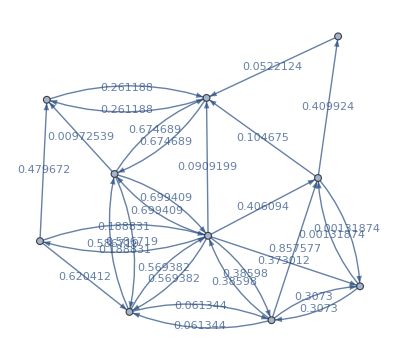

```mathematica
MixedGraphToDirectedGraph[randomMixedGraph,EdgeLabels->"EdgeWeight"]
```

```mathematica
Graph[]
```

## Documentation

### Usage

MyFunction[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Text about the example:

```mathematica
MyFunction[x,y]
```

x y

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.